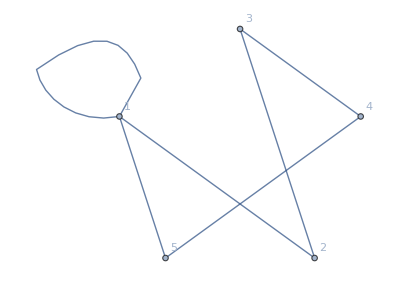

```mathematica
h= Graph[{1<->1,1<->5,1<->2, 5<->4, 2<->3, 3<->4}, VertexLabels->Automatic]
```

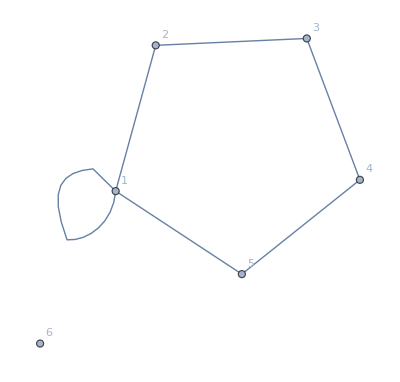

```mathematica
h1= VertexAdd[h,6]
```

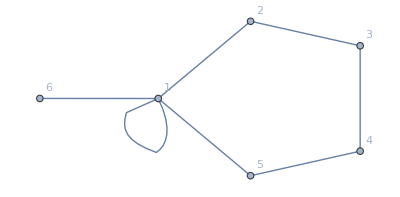

```mathematica
h2=EdgeAdd[h1, {6<->1}]
```

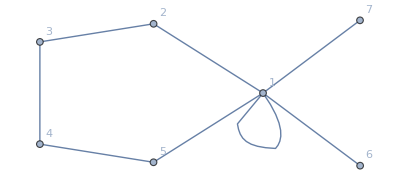

```mathematica
h3=EdgeAdd[h2, {7<->1}]
```

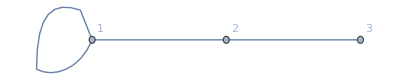

```mathematica
g1 =Subgraph[h1,{1,2,3}, VertexLabels->Automatic]
```

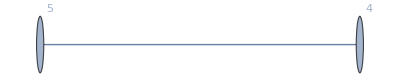

```mathematica
g2= Subgraph[h1,{4,5}, VertexLabels->Automatic]
```

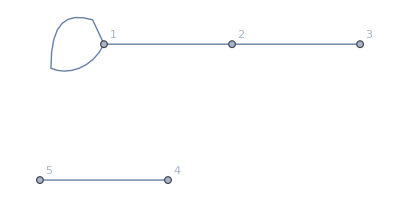

```mathematica
GraphUnion[g1, g2, VertexLabels->Automatic]
```

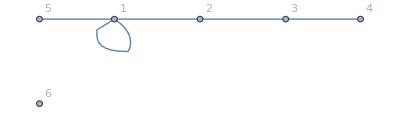

```mathematica
GraphDifference[h1,g2, VertexLabels->Automatic]
```

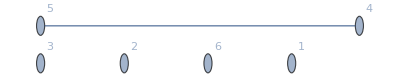

```mathematica
GraphIntersection[h1, g2, VertexLabels->Automatic]
```

```mathematica
VertexList[h1]
```

{1,5,2,4,3,6}

```mathematica
EdgeList[h1]
```

{1<->1,1<->5,1<->2,5<->4,2<->3,3<->4}

```mathematica
PlanarGraphQ[h1]
```

True

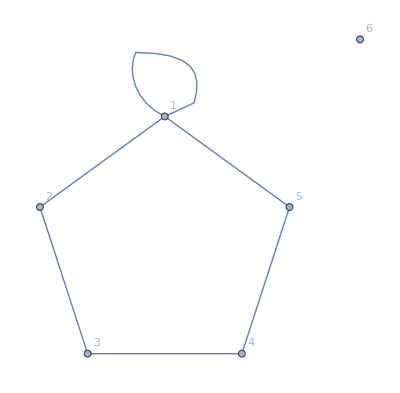

```mathematica
PlanarGraph[h1]
```

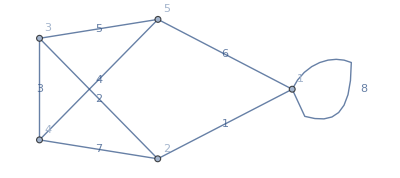

```mathematica
l1=Graph[{1<->2,2<->3, 3<->4,4<->5,3<->5,1<->5,2<->4,1<->1},VertexLabels->Automatic, EdgeWeight->Range[8], EdgeLabels->"EdgeWeight"]
```

```mathematica
f1=FindShortestPath[l1, 1, 4]
```

{1,2,3,4}

```mathematica
GraphDistance[l1, 1, 4]
```

6.

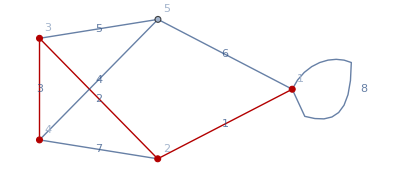

```mathematica
HighlightGraph[l1, PathGraph[f1]]
```

```mathematica
f2=FindHamiltonianCycle[l1]
```

{{1<->2,2<->4,4<->3,3<->5,5<->1}}

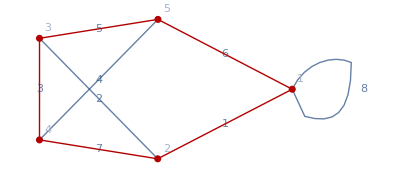

```mathematica
HighlightGraph[l1, PathGraph[f2[[1]]]]
```

```mathematica
f3=FindHamiltonianPath[l1]
```

{5,4,3,2,1}

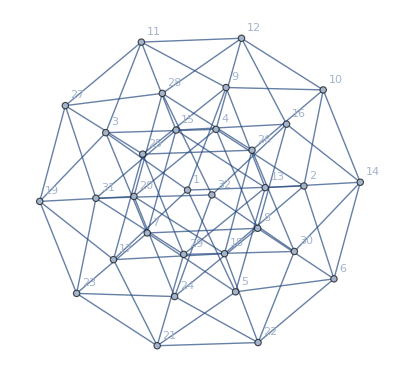

```mathematica
gg=HypercubeGraph[5,VertexLabels->Automatic]
```

```mathematica
qq = FindShortestPath[gg,10,23]
```

{10,2,1,3,7,23}

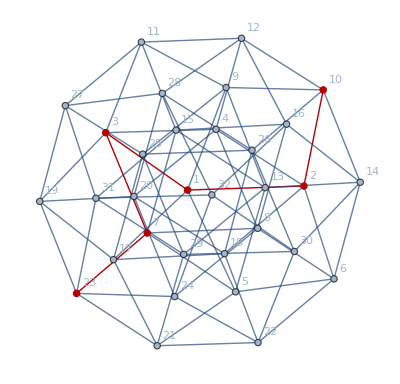

```mathematica
HighlightGraph[gg,PathGraph[qq]]
```

```mathematica
qqq=FindShortestTour[gg]
```

{32,{1,2,6,22,18,20,24,8,4,3,7,23,19,17,21,5,13,14,10,26,28,27,25,29,30,32,31,15,16,12,11,9,1}}

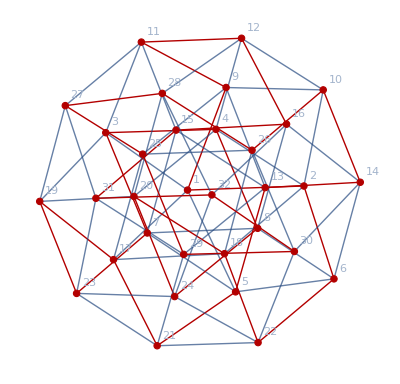

```mathematica
HighlightGraph[gg,PathGraph[qqq[[2]]]]
```

```mathematica
usa = CityData[{Large, "USA"}]
```

{New York City,Los Angeles,Chicago,Houston,Philadelphia,Phoenix,San Antonio,San Diego,Dallas,San Jose,Austin,Indianapolis,Jacksonville,San Francisco,Columbus,Fort Worth,Charlotte,Detroit,El Paso,Nashville,Seattle,Denver,Washington,Memphis,Boston,Baltimore,Oklahoma City,Portland,Las Vegas,Milwaukee,Louisville,Albuquerque,Tucson,Fresno,Sacramento,Long Beach,Kansas City,Mesa,Atlanta,Virginia Beach,Omaha,Colorado Springs,Raleigh,Miami,Oakland,Minneapolis,Tulsa,Cleveland,Wichita,New Orleans,Arlington,Honolulu,Bakersfield,Tampa,Aurora,Anaheim,Santa Ana,Corpus Christi,Riverside,Saint Louis,Lexington,Pittsburgh,Oyster Bay,Stockton,Anchorage,Cincinnati,Saint Paul,Greensboro,Toledo,Newark,Plano,Henderson,Lincoln,Orlando,Jersey City,Chula Vista,Buffalo,Fort Wayne,Chandler,Saint Petersburg,Laredo,Durham,Irvine,Madison,Norfolk,Lubbock,Gilbert,Winston-Salem,Glendale,Reno,Hialeah,Garland,Chesapeake,Irving,North Las Vegas,Scottsdale,North Hempstead,Baton Rouge,Fremont,Paradise,Richmond,Boise,San Bernardino,Birmingham,Spokane,Modesto,Des Moines,Arlington,Rochester,Oxnard,Tacoma,Fontana,Fayetteville,Moreno Valley,Augusta,Columbus,Huntington Beach,Yonkers,Montgomery,Aurora,Glendale,Shreveport,Akron,Little Rock,Amarillo,Mobile,Grand Rapids,Salt Lake City,Sunrise Manor,Huntsville,Tallahassee,Grand Prairie,Overland Park,Knoxville,Brownsville,Worcester,Newport News,Santa Clarita,Providence,Spring Valley,Fort Lauderdale,Garden Grove,Oceanside,Rancho Cucamonga,Santa Rosa,Port Saint Lucie,Chattanooga,Tempe,Jackson,Cape Coral,Vancouver,Ontario,Sioux Falls,Peoria,Springfield,Pembroke Pines,Elk Grove,Salem,Corona,Lancaster,Eugene,Palmdale,McKinney,Salinas,Fort Collins,Cary,Hayward,Springfield,Pasadena,Pomona,Alexandria,Escondido,Sunnyvale,Lakewood,Kansas City,Rockford,Torrance,Hollywood,Joliet,Bridgeport,Clarksville,Paterson,Naperville,Frisco,Mesquite,Savannah,Syracuse,Dayton,Pasadena,Orange,Fullerton,McAllen,Metairie,Killeen,Hampton,Bellevue,Warren,Miramar,West Valley City,Ramapo,Olathe,Columbia,Sterling Heights,Thornton,New Haven,Waco,Charleston,Thousand Oaks,Visalia,Cedar Rapids,Elizabeth,Roseville,Gainesville,Carrollton,Stamford,Denton,Midland,Coral Springs,Concord,Topeka,Simi Valley,East Los Angeles,Surprise,Lafayette,Kent,Amherst,Hartford,Santa Clara,Victorville,Abilene,Murfreesboro,Athens,Evansville,Vallejo,Allentown,Berkeley,Norman,Ann Arbor,Beaumont,Independence,Columbia,Springfield,El Monte,Fargo,Peoria,Provo,Lansing,Odessa,Downey,Wilmington,Arvada,Costa Mesa,Round Rock,Carlsbad,Westminster,Inglewood,Rochester,Fairfield,Elgin,West Jordan,Clearwater,Manchester,Lowell,Gresham,Cambridge,San Buenaventura (Ventura),Temecula,Waterbury,Antioch,Billings,High Point,Richardson,Richmond,Enterprise,West Covina,Pueblo,Murrieta,Centennial,Norwalk,North Charleston,Everett,Pompano Beach,Daly City,Palm Bay,Burbank,Wichita Falls,Boulder,Green Bay,Broken Arrow,West Palm Beach,Brandon,College Station,Pearland,Santa Maria,El Cajon,San Mateo,Lewisville,Rialto,Davenport,Lakeland,Clovis,Edison,Sandy Springs,Tyler,Las Cruces,South Bend}

```mathematica
pos =GeoPosition[CityData[#,"Coordinates"]]& /@usa;
```

```mathematica
f= FindShortestTour[pos, 1,2]
```

{38178.2 km,{1,75,70,211,302,5,235,182,200,118,97,63,215,180,205,268,227,168,136,139,25,265,263,262,187,109,226,77,48,123,62,26,108,23,171,101,137,195,85,40,93,250,113,43,166,82,68,271,88,17,134,147,303,39,232,115,202,280,207,186,13,213,74,284,146,290,218,282,141,178,198,44,91,156,150,300,291,54,80,261,131,116,119,104,130,231,20,181,233,31,61,66,15,188,12,78,69,18,203,197,238,247,127,306,3,179,183,120,259,176,84,30,288,257,67,46,244,153,73,41,107,210,299,245,242,60,241,155,240,37,175,201,133,220,49,47,289,27,237,286,16,51,132,9,94,214,297,216,163,184,71,272,92,185,304,122,124,24,149,126,50,193,98,224,239,169,293,4,292,58,135,192,81,7,11,253,194,206,230,125,86,217,248,19,305,32,276,42,278,55,22,174,251,204,255,287,165,270,128,246,260,199,102,105,264,161,158,28,151,111,225,21,196,281,65,52,145,258,269,219,234,273,236,45,14,283,296,167,173,99,228,10,164,106,64,157,35,212,90,301,34,209,53,294,266,110,208,221,138,160,162,285,121,189,222,243,275,170,152,144,112,298,103,229,274,140,29,95,129,100,72,223,154,89,6,96,148,79,87,38,33,76,295,8,172,254,143,267,277,114,59,159,190,83,252,117,142,57,56,191,279,249,36,177,256,2}}

```mathematica
GeoGraphics[{Thick, Red, GeoPath[pos[[f[[2]] ]] ]}]
```

-Graphics-

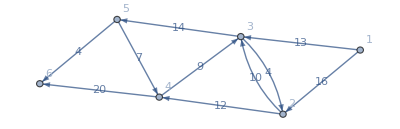

```mathematica
ff=Graph[{1,2,3,4,5, 6}, {1->2,2->3,3->2,1->3,2->4,4->3,4->6,3->5,5->4,5->6}, VertexLabels->Automatic, EdgeCapacity->{16,10,4,13,12,9,20,14,7,4}, EdgeWeight->{16,10,4,13,12,9,20,14,7,4}, EdgeLabels->"EdgeWeight"]
```

```mathematica
FindMaximumFlow[ff,1,6]
```

23

```mathematica
data=FindMaximumFlow[ff,1,6, "OptimumFlowData"]
```

OptimumFlowData[<6>, <8>]

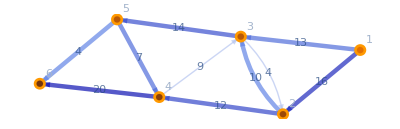

```mathematica
data["FlowGraph"]
```

```mathematica
Grid[{#,data[#]}&/@data["EdgeList"], Frame->All]
```

1->2 | 16
1->3 | 7
2->3 | 4
2->4 | 12
3->5 | 11
4->6 | 19
5->4 | 7
5->6 | 4

```mathematica
data["FlowMatrix"] //MatrixForm
```

(0 | 16 | 7 | 0 | 0 | 0
0 | 0 | 4 | 12 | 0 | 0
0 | 0 | 0 | 0 | 11 | 0
0 | 0 | 0 | 0 | 0 | 19
0 | 0 | 0 | 7 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0)